The following show that the two positions of the same energy will have equal mutual transfer prob.

```mathematica
Clear["Global`*"];
```

```mathematica
SeedRandom[0]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
HessianH[f_,x_List?VectorQ]:=D[f,{x,2}]
```

```mathematica
GradientG[f_,x_List?VectorQ]:=D[f,{x,1}]
```

```mathematica
ρ=0.9;
```

```mathematica
SIGMA={{1/ρ,ρ},{ρ,1/ρ}};
```

```mathematica
U[x_,y_]=1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]];
```

```mathematica
dU[x_,y_]=GradientG[U[x,y],{x,y}];
```

```mathematica
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
```

```mathematica
K[p1_,p2_,q1_,q2_]:=1/2{p1,p2}. LinearSolve[ddU[q1,q2],{p1,p2}]
```

```mathematica
dK[x_,y_]=GradientG[K[x,y],{x,y}];
```

Equal prob. tranfer of two points of same total energy

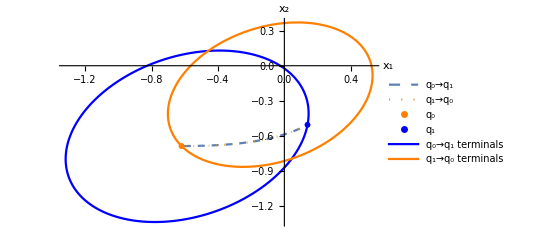

```mathematica
Dim=2;
vanilla=True;
angles=1000;
q0=RandomVariate[NormalDistribution[0,1],Dim];
H=Apply[U,q0]+1;traj[U_,dU_,ddU_,q0_,k0_,qq_]:=Module[{ND=NormalDistribution[0,1],q,dt=0.01,p0,p,p00={0,0},dist=Infinity,
QS=List[]},
For[i=1,i≤angles,i++,
q=q0;
p0={Cos[(2π i)/angles],Sin[(2π i)/angles]};
p0=If[vanilla,√2 p0/Norm[p0] √k0,p0/(√K[p0[[1]],p0[[2]],q[[1]],q[[2]]])√k0];
p=p0;
For[j=1,j⩽60,j++,
p=p-dt Apply[dU,q];
q=q+dt If[vanilla, p,  LinearSolve[Apply[ddU,q],p]]];
If[Length[qq]≠0 &&Norm[qq-q]<dist,dist=Norm[qq-q];p00=p0];
QS=Append[QS,q]];
{QS,p0,p00}];
traj1[U_,dU_,ddU_,p0_,q0_]:=Module[{ND=NormalDistribution[0,1],p,q,dt=0.01,
QS=List[]},
q=q0;p=p0;
For[j=1,j⩽60,j++,
p=p-dt Apply[dU,q];
q=q+dt If[vanilla, p,  LinearSolve[Apply[ddU,q],p]];QS=Append[QS,q]];
QS];
t=traj[U,dU,ddU,q0,1,{}];
QS1=t[[1]];
p0=t[[2]];
t=traj[U,dU,ddU,QS1[[-1]],H-Apply[U,QS1[[-1]]],q0];
q1=QS1[[-1]];
QS2=t[[1]];
p00=t[[3]];
QS3=traj1[U,dU,ddU,p0,q0];
QS4=traj1[U,dU,ddU,p00,q1];
QS1=Append[QS1,QS1[[1]]];
QS2=Append[QS2,QS2[[1]]];
Print["Equal prob. tranfer of two points of same total energy"]
ListPlot[{QS3,QS4,{q0},{q1},QS1,QS2},AxesLabel->{"x_1","x_2"},PlotMarkers->{None,None,"OpenMarkers","OpenMarkers", None,None ,None},PlotLegends->{"q_0→q_1","q_1→q_0","q_0","q_1","q_0→q_1 terminals","q_1→q_0 terminals"},Joined->{True,True,False,False,True,True},PlotStyle->{Dashed,Dotted,Orange,Blue,Blue,Orange}]
```

Thread::tdlen: Objects of unequal length in {-0.60602,-0.68131} ； {{-0.60602,-0.68131}} cannot be combined.

Thread::tdlen: Objects of unequal length in {-0.579047,-0.672322} ； {{-0.60602,-0.68131},{-0.592539,-0.676842},{-0.579047,-0.672322}} cannot be combined.

Thread::tdlen: Objects of unequal length in {-0.565545,-0.667749} ； {{-0.60602,-0.68131},{-0.592539,-0.676842},{-0.579047,-0.672322},{-0.565545,-0.667749}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

trajectories with constant total energy from a position

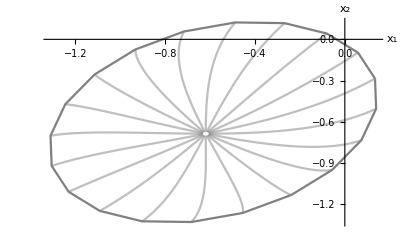

```mathematica
points=20;
vanilla=True;traj2[U_,dU_,ddU_,q0_,k0_]:=Module[{ND=NormalDistribution[0,1],q,dt=0.01,p0,p,p00={0,0},dist=Infinity,
QS=List[],qs},
For[i=1,i≤points,i++,
q=q0;
p0={Cos[(2π i)/points],Sin[(2π i)/points]};
p0=If[vanilla,√2 p0/Norm[p0] √k0,p0/(√K[p0[[1]],p0[[2]],q[[1]],q[[2]]])√k0];
p=p0;
qs=List[]；
For[j=1,j⩽60,j++,
p=p-dt Apply[dU,q];
q=q+dt If[vanilla, p,  LinearSolve[Apply[ddU,q],p]]；
qs=Append[qs,q]];
QS=AppendTo[QS,qs]];
QS];
QS5=traj2[U,dU,ddU,q0,1];
endpoints=Table[QS5[[i]][[-1]],{i,1,points}];
endpoints=Append[endpoints,endpoints[[1]]];
l1=ListPlot[Table[QS5[[i]],{i,1,points}],Joined->True,PlotStyle->Directive[Gray,Opacity[.5]],AxesLabel->{"x_1","x_2"}];l2=ListPlot[endpoints,Joined->True,PlotStyle->Gray];
Print["trajectories with constant total energy from a position"];
Show[l1,l2]
```